```mathematica
(*
	(c) 2011 Alex Kontorovich

	This file complements the expository note on an arithmetic surface
*)
```

```mathematica
(* 
	Defining quaternions as matrices
*)
EE={{1,0},{0,1}};
II=3^(1/2){{1,0},{0,-1}};
JJ=3^(1/2){{0,-1},{-1,0}};
KK=1/3II.JJ;
```

```mathematica
(* 
	The general form of a quaternion
*)
u=(aa EE + bb II + cc JJ+ dd KK);
u//MatrixForm
```

(aa+√3 bb | -√3 cc-dd
-√3 cc+dd | aa-√3 bb)

```mathematica
Det[u]
```

aa^2-3 bb^2-3 cc^2+dd^2

```mathematica
?SquaresR
```

RowBox[{"SquaresR", "[", RowBox[{StyleBox["d", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives the number of ways RowBox[{SubscriptBox[StyleBox["r", "TI"], StyleBox["d", "TI"]], "(", StyleBox["n", "TI"], ")"}] to represent the integer StyleBox["n", "TI"] as a sum of StyleBox["d", "TI"] squares.

```mathematica
(* Main param *)
Q=100;

(* get table, for each n of reps a^2+d^2=n, with 0≤ d<a *)
sumsq=Table[{},{j,1,Q}];
For[a=0,a≤Sqrt[Q],a++,
For[d=a+1,d≤Sqrt[Q],d++,
If[a^2+d^2≤Q,
AppendTo[sumsq[[a^2+d^2]],{a,d}];
];
];
];
For[a=1,a≤Sqrt[Q]/2,a++,
AppendTo[sumsq[[2a^2]],{a,a}];
];
```

```mathematica
(* norm one elements of division algebra are a^2+d^2=1+3(b^2+c^2), or n=1+3m, with n, m sums of two squares  *)
normElts={{1,0,0,0},{0,0,0,1}}; (* identity and elliptic element *)
For [m=1,m≤(Q-1)/3,m++,
bcS=sumsq[[m]]; (* write m as sum of squares in as many ways as possible (maybe none) *)
For[j=1,j≤Length[bcS],j++,
adS=sumsq[[1+3m]]; (* write n=1+3m as sum of squares in as many ways as possible *)
For[k=1,k≤Length[adS],k++,

(* now have a,b,c,d up to permutations and +/- *)

If[adS[[k,1]]==adS[[k,2]],
(* here a=d and hence b≠c, since 2a^2 = 1 + 3 (2b^2) has no solution *)
For[sig1=-1,sig1≤1,sig1+=2,
For[sig2=-1,sig2≤1,sig2+=2,
For[sig3=-1,sig3≤1,sig3+=2,

AppendTo[normElts,{adS[[k,1]],sig1 bcS[[j,1]],sig2 bcS[[j,2]],sig3 adS[[k,1]] }];
AppendTo[normElts,{adS[[k,1]],sig1 bcS[[j,2]],sig2 bcS[[j,1]],sig3 adS[[k,1]] }];
];
];
];

,
If[bcS[[j,1]]==bcS[[j,2]],
(* here a≠d but b=c *)

For[sig1=-1,sig1≤1,sig1+=2,
For[sig2=-1,sig2≤1,sig2+=2,
For[sig3=-1,sig3≤1,sig3+=2,

AppendTo[normElts,{adS[[k,1]],sig1 bcS[[j,1]],sig2 bcS[[j,1]],sig3 adS[[k,2]] }];
AppendTo[normElts,{adS[[k,2]],sig1 bcS[[j,1]],sig2 bcS[[j,1]],sig3 adS[[k,1]] }];
];
];
];



,
(* here a≠d and b≠c *)

For[sig1=-1,sig1≤1,sig1+=2,
For[sig2=-1,sig2≤1,sig2+=2,
For[sig3=-1,sig3≤1,sig3+=2,

AppendTo[normElts,{adS[[k,1]],sig1 bcS[[j,1]],sig2 bcS[[j,2]],sig3 adS[[k,2]] }];
AppendTo[normElts,{adS[[k,2]],sig1 bcS[[j,1]],sig2 bcS[[j,2]],sig3 adS[[k,1]] }];
AppendTo[normElts,{adS[[k,1]],sig1 bcS[[j,2]],sig2 bcS[[j,1]],sig3 adS[[k,2]] }];
AppendTo[normElts,{adS[[k,2]],sig1 bcS[[j,2]],sig2 bcS[[j,1]],sig3 adS[[k,1]] }];
];
];
];
];
];



];
];
];
```

```mathematica
normElts//Length
```

274

```mathematica
(* 
	This turns solutions into matrices 
*)
listToMat[list_]:=
Simplify[u/.{aa->list[[1]],bb->list[[2]],cc->list[[3]],dd->list[[4]]}];
```

```mathematica
(*
	Now we have 2x2 matrices in SL(2,R)
*)
Gammas=listToMat/@normElts;
Length[Gammas]
```

274

```mathematica
(*
	We now construct a Dirichlet domain corresponding to the action of the above matrices on some base point
*)
```

```mathematica
(* Pick a point *)
basept=I;
(* Action of SL(2,R) on H *)
zTogz[z_,g_]:=Simplify[Re[(g[[1,1]]z+g[[1,2]])/(g[[2,1]]z+g[[2,2]])]+I  Im[(g[[1,1]]z+g[[1,2]])/(g[[2,1]]z+g[[2,2]])]];
(* Going between C and R^2 *)
CtoVect[z_]:={Re[z],Im[z]};
VectToC[p_]:=p[[1]]+I p[[2]];

(* Action of matrix on basept *)
MatTimesBase[mat_]:=zTogz[basept,mat];
(* This is the orbit of Gammas found above on basept *)
OrbitAll=MatTimesBase/@N[Gammas];
```

```mathematica
Length[OrbitAll]
```

274

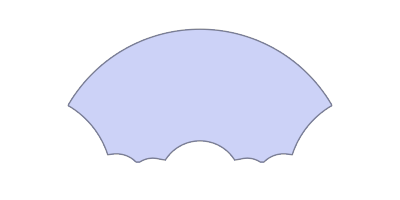
```mathematica
regPic=-Graphics-;
```

```mathematica
(* Lets see the full orbit *)
CptsAll=Simplify[CtoVect/@OrbitAll];
ptsPicAll=ListPlot[CptsAll,PlotRange->All];
```

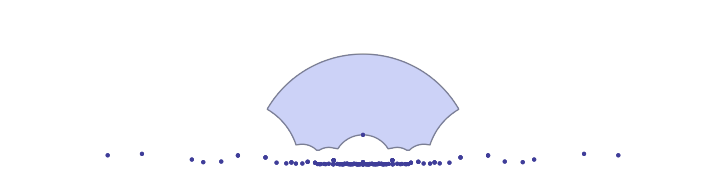

```mathematica
pic=Show[regPic,ptsPicAll,PlotRange->{{-10,10},{0,5}}]
```

```mathematica
?ContourPlot
```

RowBox[{"ContourPlot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a contour plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] and StyleBox["y", "TI"]. 
RowBox[{"ContourPlot", "[", RowBox[{RowBox[{StyleBox["f", "TI"], "==", StyleBox["g", "TI"]}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots contour lines for which RowBox[{StyleBox["f", "TI"], "=", StyleBox["g", "TI"]}]. 
RowBox[{"ContourPlot", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], "==", SubscriptBox[StyleBox["g", "TI"], StyleBox["1", "TR"]]}], ",", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], "==", SubscriptBox[StyleBox["g", "TI"], StyleBox["2", "TR"]]}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several contour lines.

```mathematica
TwoCoshDis[z_,w_]:=2+Abs[z-w]^2/(Im[z] Im[w]);
```

```mathematica
FullSimplify[TwoCoshDis[I,x+I y]==q,Assumptions->x>0&&y>0]
```

1+x^2+y^2==q y

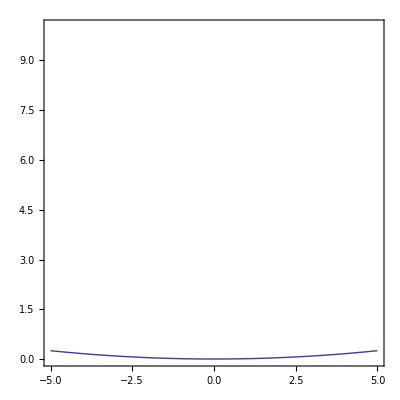

```mathematica
ContourPlot[1+x^2+y^2==Q y,{x,-5,5},{y,0,10}]
```

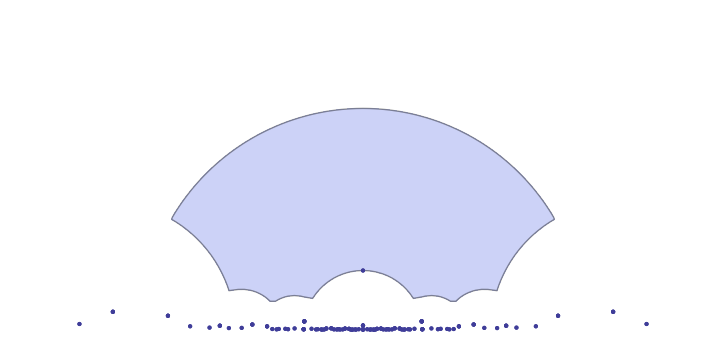

```mathematica
pic=Show[regPic,


ptsPicAll,
(*
ContourPlot[1+x^2+y^2==100 y,{x,-10,10},{y,0,10},ContourStyle->{Red,Thick}],
*)
PlotRange->{{-5,5},{0,5}}]
```

```mathematica
?Circle
```

RowBox[{"Circle", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], ",", StyleBox["r", "TI"]}], "]"}] is a two-dimensional graphics primitive that represents a circle of radius StyleBox["r", "TI"] centered at the point StyleBox["x", "TI"], StyleBox["y", "TI"]. 
RowBox[{"Circle", "[", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], "]"}] gives a circle of radius 1. 
RowBox[{"Circle", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], ",", StyleBox["r", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["θ", "TR"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["θ", "TR"], StyleBox["2", "TR"]]}], "}"}]}], "]"}] gives a circular arc. 
RowBox[{"Circle", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["r", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["r", "TI"], StyleBox["y", "TI"]]}], "}"}]}], "]"}] gives an ellipse with semi-axes of lengths SubscriptBox[StyleBox["r", "TI"], StyleBox["x", "TI"]] and SubscriptBox[StyleBox["r", "TI"], StyleBox["y", "TI"]], oriented parallel to the coordinate axes.

```mathematica
Solve[{
(x-z1)^2+z2^2==r^2,
(x-w1)^2+w2^2==r^2
},{x,r}]
```

{{x→(w1^2+w2^2-z1^2-z2^2)/(2 (w1-z1)),r→-1/(2 √(w1^2-2 w1 z1+z1^2))(√(w1^4+2 w1^2 w2^2+w2^4-4 w1^3 z1-4 w1 w2^2 z1+6 w1^2 z1^2+2 w2^2 z1^2-4 w1 z1^3+z1^4+2 w1^2 z2^2-2 w2^2 z2^2-4 w1 z1 z2^2+2 z1^2 z2^2+z2^4))},{x→(w1^2+w2^2-z1^2-z2^2)/(2 (w1-z1)),r→1/(2 √(w1^2-2 w1 z1+z1^2))(√(w1^4+2 w1^2 w2^2+w2^4-4 w1^3 z1-4 w1 w2^2 z1+6 w1^2 z1^2+2 w2^2 z1^2-4 w1 z1^3+z1^4+2 w1^2 z2^2-2 w2^2 z2^2-4 w1 z1 z2^2+2 z1^2 z2^2+z2^4))}}

```mathematica
w1^4+2 w1^2 w2^2+w2^4-4 w1^3 z1-4 w1 w2^2 z1+6 w1^2 z1^2+2 w2^2 z1^2-4 w1 z1^3+z1^4+2 w1^2 z2^2-2 w2^2 z2^2-4 w1 z1 z2^2+2 z1^2 z2^2+z2^4//Factor
```

(w1^2+w2^2-2 w1 z1+z1^2-2 w2 z2+z2^2) (w1^2+w2^2-2 w1 z1+z1^2+2 w2 z2+z2^2)

```mathematica
(w1+w2 I- z1 + z2 I)(w1-w2 I- z1-z2 I)//Expand
```

w1^2+w2^2-2 w1 z1+z1^2+2 w2 z2+z2^2

```mathematica
(w1+w2 I - z1 -z2 I)(w1-w2 I - z1+z2 I)//Expand
```

w1^2+w2^2-2 w1 z1+z1^2-2 w2 z2+z2^2

```mathematica
(* Now to construct geodesics. *)
geod[z_,w_]:=Module[{x,r,gt1,gt2,ans},
If[Re[z]==Re[w],
(* vertical geod *)
ans=Line[{CtoVect[z],CtoVect[w]}];
,
(* otherwise circle *)
x=(Abs[w]^2-Abs[z]^2)/(2 (Re[w]-Re[z]));
r=(Abs[w-z] Abs[w-Conjugate[z]])/(2Abs[Re[w]-Re[z]]);
If[Re[z]≠x,
gt1=ArcTan[Im[z]/(Re[z]-x)];
If[gt1<0,gt1+=Pi];
,
gt1=Pi/2;
];
If[Re[w]≠x,
gt2=ArcTan[Im[w]/(Re[w]-x)];
If[gt2<0,gt2+=Pi];
,
gt2=Pi/2;
];
ans=Circle[{x,0},r,{gt1,gt2}];
];
ans
];
geodToBase[z_]:=geod[z,basept];
```

0.989743+0.142857 ⅈ

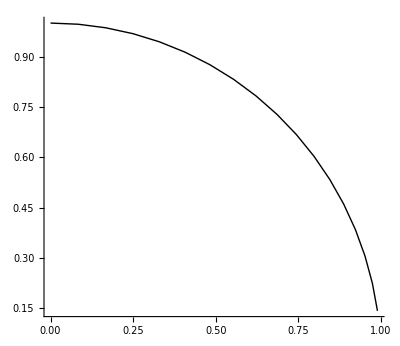

```mathematica
OrbitAll[[4]]
Show[%//geodToBase//Graphics,AxesOrigin->{0,0},Axes->True]
```

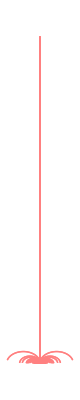

```mathematica
geodPic=Show[Graphics[{Thin,Pink,geodToBase/@OrbitAll}]]
```

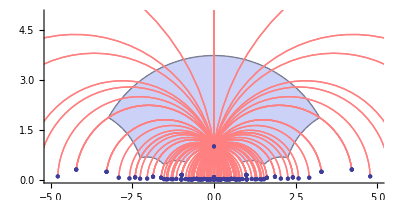

```mathematica
pic=Show[regPic,

geodPic,
ptsPicAll,

PlotRange->{{-5,5},{0,5}},Axes->True]
```

```mathematica
(* Main param *)
Q=1000;
X=Q^2/8  


(* get table, for each n of reps a^2+d^2=n, with 0≤ d<a *)
sumsq=Table[{},{j,1,X}];
For[a=0,a≤Sqrt[X],a++,
For[d=a+1,d≤Sqrt[X],d++,
If[a^2+d^2≤X,
AppendTo[sumsq[[a^2+d^2]],{a,d}];
];
];
];
For[a=1,a≤Sqrt[X]/2,a++,
AppendTo[sumsq[[2a^2]],{a,a}];
];
```

125000

```mathematica
(* norm one elements of division algebra are a^2+d^2=1+3(b^2+c^2), or n=1+3m, with n, m sums of two squares  *)
normElts={{1,0,0,0},{0,0,0,1}}; (* identity and elliptic element *)
For [m=1,m≤(X-1)/3,m++,
bcS=sumsq[[m]]; (* write m as sum of squares in as many ways as possible (maybe none) *)
For[j=1,j≤Length[bcS],j++,
adS=sumsq[[1+3m]]; (* write n=1+3m as sum of squares in as many ways as possible *)
For[k=1,k≤Length[adS],k++,

(* now have a,b,c,d up to permutations and +/- *)

If[adS[[k,1]]==adS[[k,2]],
(* here a=d and hence b≠c, since 2a^2 = 1 + 3 (2b^2) has no solution *)
For[sig1=-1,sig1≤1,sig1+=2,
For[sig2=-1,sig2≤1,sig2+=2,
For[sig3=-1,sig3≤1,sig3+=2,

AppendTo[normElts,{adS[[k,1]],sig1 bcS[[j,1]],sig2 bcS[[j,2]],sig3 adS[[k,1]] }];
AppendTo[normElts,{adS[[k,1]],sig1 bcS[[j,2]],sig2 bcS[[j,1]],sig3 adS[[k,1]] }];
];
];
];

,
If[bcS[[j,1]]==bcS[[j,2]],
(* here a≠d but b=c *)

For[sig1=-1,sig1≤1,sig1+=2,
For[sig2=-1,sig2≤1,sig2+=2,
For[sig3=-1,sig3≤1,sig3+=2,

AppendTo[normElts,{adS[[k,1]],sig1 bcS[[j,1]],sig2 bcS[[j,1]],sig3 adS[[k,2]] }];
AppendTo[normElts,{adS[[k,2]],sig1 bcS[[j,1]],sig2 bcS[[j,1]],sig3 adS[[k,1]] }];
];
];
];



,
(* here a≠d and b≠c *)

For[sig1=-1,sig1≤1,sig1+=2,
For[sig2=-1,sig2≤1,sig2+=2,
For[sig3=-1,sig3≤1,sig3+=2,

AppendTo[normElts,{adS[[k,1]],sig1 bcS[[j,1]],sig2 bcS[[j,2]],sig3 adS[[k,2]] }];
AppendTo[normElts,{adS[[k,2]],sig1 bcS[[j,1]],sig2 bcS[[j,2]],sig3 adS[[k,1]] }];
AppendTo[normElts,{adS[[k,1]],sig1 bcS[[j,2]],sig2 bcS[[j,1]],sig3 adS[[k,2]] }];
AppendTo[normElts,{adS[[k,2]],sig1 bcS[[j,2]],sig2 bcS[[j,1]],sig3 adS[[k,1]] }];
];
];
];
];
];



];
];
];
```

```mathematica
normElts//Length
```

253506

```mathematica
(* 
	This turns solutions into matrices 
*)
listToMat[list_]:=
Simplify[u/.{aa->list[[1]],bb->list[[2]],cc->list[[3]],dd->list[[4]]}];
```

```mathematica
(*
	Now we have 2x2 matrices in SL(2,R)
*)
Gammas=listToMat/@normElts;
Length[Gammas]
```

253506

```mathematica
normSq[mat_]:=N[Tr[mat.Transpose[mat]]];
```

```mathematica
normSq[Gammas[[41]]]
```

50.

```mathematica
?Save
```

Save[filename,symbol] appends definitions associated with the specified symbol to a file. 
Save[filename,form] appends definitions associated with all symbols whose names match the string pattern form. 
Save[filename,context`] appends definitions associated with all symbols in the specified context. 
Save[filename,{object_1,object_2,…}] appends definitions associated with several objects.

```mathematica
Save["Gammas.m",Gammas]
```

```mathematica
GammasSorted=Sort[Gammas,normSq[#1]<normSq[#2]&];
```

```mathematica
Save["GammasSorted.m",GammasSorted]
```

```mathematica
norms=Sqrt[normSq/@GammasSorted];
```

```mathematica
Save["norms.m",norms]
```

```mathematica
ListPlot[norms]
```

-Graphics-

```mathematica
?Fit
```

RowBox[{"Fit", "[", RowBox[{StyleBox["data", "TI"], ",", StyleBox["funs", "TI"], ",", StyleBox["vars", "TI"]}], "]"}] finds a least-squares fit to a list of data as a linear combination of the functions StyleBox["funs", "TI"] of variables StyleBox["vars", "TI"].

```mathematica
fconst=Fit[norms,Sqrt[x],x]/Sqrt[x]
```

1.39848

```mathematica
vol= Pi Fit[norms,Sqrt[x],x]^2/x
```

6.14416

```mathematica
Show[ListPlot[norms],Plot[fconst Sqrt[x],{x,0,Length[norms]},PlotStyle->Directive[Thick,Red]]]
```

-Graphics-

```mathematica
GammasSmall=Select[GammasSorted,normSq[#]<100^2&];
```

```mathematica
Length[GammasSmall]
```

5554

```mathematica
normsSm=Sqrt[normSq/@GammasSmall];
fconstSm=Fit[normsSm,Sqrt[x],x]/Sqrt[x]
```

1.31625

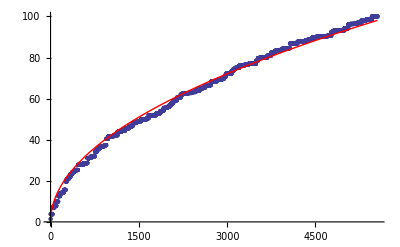

```mathematica
Show[ListPlot[normsSm],Plot[fconstSm Sqrt[x],{x,0,Length[normsSm]},PlotStyle->Directive[Thick,Red]]]
```

```mathematica
(* Get angles *)
```

```mathematica
(* g_2(xi) = 1/(4 pi) #{(g,g'): 2Pi xi/tot <|gt_g-gt_g'|<2Pi(xi+1)/tot} *)
```